```mathematica
ChromaticPolynomial[VertexDelete[Graph[plantri[[2]]],12],4]/24
```

40

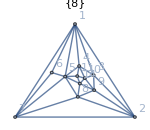
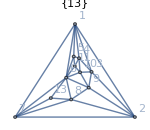
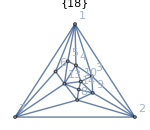
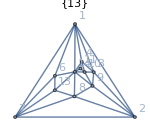
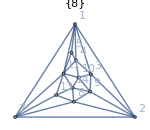
{{-Graphics-, | 5 | 6 | 11 | 14
5 | 8
0 | 0
8 | 0
8 | 0
8
6 |  | 8
0 | 2
6 | 3
5
11 |  |  | 8
0 | 0
8
14 |  |  |  | 8
0}5<->13,{-Graphics-, | 5 | 6 | 11 | 13
5 | 13
0 | 0
13 | 0
13 | 3
10
6 |  | 13
0 | 0
13 | 0
13
11 |  |  | 13
0 | 6
7
13 |  |  |  | 13
0}6<->14,{-Graphics-, | 5 | 6 | 13 | 14
5 | 18
0 | 0
18 | 0
18 | 6
12
6 |  | 18
0 | 0
18 | 6
12
13 |  |  | 18
0 | 0
18
14 |  |  |  | 18
0}13<->11,{-Graphics-, | 6 | 11 | 13 | 14
6 | 13
0 | 3
10 | 0
13 | 0
13
11 |  | 13
0 | 6
7 | 0
13
13 |  |  | 13
0 | 0
13
14 |  |  |  | 13
0}14<->5,{-Graphics-, | 5 | 11 | 13 | 14
5 | 8
0 | 0
8 | 2
6 | 3
5
11 |  | 8
0 | 0
8 | 0
8
13 |  |  | 8
0 | 0
8
14 |  |  |  | 8
0}11<->6}

```mathematica
Table[
With[
{g=VertexContract[VertexDelete[Graph[plantri[[2]]],12],{edge[[1]],edge[[2]]}]},
Labeled[ColorMainMatrix17[g,Graph[#,VertexLabels->"Name",GraphLayout->If[PlanarGraphQ[#],"TutteEmbedding","SpringElectricalEmbedding"],PlotLabel->{ChromaticPolynomial[#,4]/24},ImageSize->150]&,Select[{5,6,13,14,11},#≠edge[[2]]&]],
edge]
]
,{edge,{5<->13,6<->14,13<->11,14<->5,11<->6}}]
```

```mathematica
ChromaticPolynomial[VertexDelete[Graph[plantri[[1]]],1],4]/24
```

20

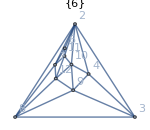
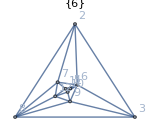
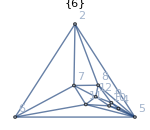
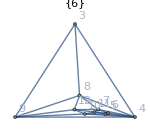
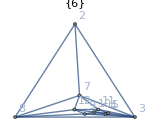
{{-Graphics-, | 2 | 3 | 4 | 6
2 | 6
0 | 0
6 | 0
6 | 0
6
3 |  | 6
0 | 0
6 | 2
4
4 |  |  | 6
0 | 2
4
6 |  |  |  | 6
0}2<->5,{-Graphics-, | 2 | 3 | 5 | 6
2 | 6
0 | 0
6 | 2
4 | 0
6
3 |  | 6
0 | 2
4 | 0
6
5 |  |  | 6
0 | 0
6
6 |  |  |  | 6
0}6<->4,{-Graphics-, | 2 | 4 | 5 | 6
2 | 6
0 | 2
4 | 0
6 | 0
6
4 |  | 6
0 | 0
6 | 2
4
5 |  |  | 6
0 | 0
6
6 |  |  |  | 6
0}5<->3,{-Graphics-, | 3 | 4 | 5 | 6
3 | 6
0 | 0
6 | 2
4 | 2
4
4 |  | 6
0 | 0
6 | 0
6
5 |  |  | 6
0 | 0
6
6 |  |  |  | 6
0}4<->2,{-Graphics-, | 2 | 3 | 4 | 5
2 | 6
0 | 0
6 | 2
4 | 2
4
3 |  | 6
0 | 0
6 | 0
6
4 |  |  | 6
0 | 0
6
5 |  |  |  | 6
0}3<->6}

```mathematica
Table[
With[
{g=VertexContract[VertexDelete[Graph[plantri[[1]]],1],{edge[[1]],edge[[2]]}]},
Labeled[ColorMainMatrix17[g,Graph[#,VertexLabels->"Name",GraphLayout->If[PlanarGraphQ[#],"TutteEmbedding","SpringElectricalEmbedding"],PlotLabel->{ChromaticPolynomial[#,4]/24},ImageSize->150]&,Select[{2,3,4,5,6},#≠edge[[2]]&]],
edge]
]
,{edge,{2<->5,6<->4,5<->3,4<->2,3<->6}}]
```

```mathematica
With[
{g=Graph[plantri[[3]]]},
Table[{v,VertexDegree[g,v],VertexList[NeighborhoodGraph[g,v]]},{v,VertexList[g]}]
]
```

{{1,6,{1,2,3,4,5,6,7}},{2,5,{2,1,3,7,8,9}},{3,5,{3,1,2,4,9,10}},{4,5,{4,1,3,5,10,11}},{5,5,{5,1,4,6,11,12}},{6,5,{6,1,5,7,12,13}},{7,5,{7,1,2,6,8,13}},{8,6,{8,2,7,9,13,14,15}},{9,5,{9,2,3,8,10,15}},{10,5,{10,3,4,9,11,15}},{11,6,{11,4,5,10,12,14,15}},{12,5,{12,5,6,11,13,14}},{13,5,{13,6,7,8,12,14}},{14,5,{14,8,11,12,13,15}},{15,5,{15,8,9,10,11,14}}}

```mathematica
ChromaticPolynomial[VertexDelete[Graph[plantri[[3]]],2],4]/24
```

48

```mathematica
ChromaticPolynomial[Graph[plantri[[3]]],4]/24
```

32

```mathematica
Table[
With[
{g=VertexContract[VertexDelete[Graph[plantri[[3]]],2],{edge[[1]],edge[[2]]}]},
Labeled[ChromaticPolynomial[g,4]/24,
edge]
]
,{edge,Rule3Cycle[{1,3,7,8,9}]}]
```

{191<->3,143<->7,187<->8,198<->9,181<->9}